```mathematica
GE0data=Import["~/Research/SIR/Source/FRO_adm0.kmz","Data"];
```

```mathematica
GE1data=Import["~/Research/SIR/Source/FRO_adm1.kmz","Data"];
```

```mathematica
GE2data=Import["~/Research/SIR/Source/FRO_adm1.kmz","Data"];
```

```mathematica
names0=Flatten["PlacemarkNames"/.GE0data]
```

{Faroe Islands}

```mathematica
names1= Flatten["PlacemarkNames"/.GE1data]
```

{Eysturoyar,Norderøerne,Sandoyar,Streymoyar,Suðuroyar,Vågø}

```mathematica
names2=Flatten["PlacemarkNames"/.GE2data]
```

{Eysturoyar,Norderøerne,Sandoyar,Streymoyar,Suðuroyar,Vågø}

```mathematica
(Geom0=Flatten["Geometry"/.GE0data])//Length
```

26

```mathematica
(Geom1=Flatten["Geometry"/.GE1data])//Length
```

27

```mathematica
(Geom2=Flatten["Geometry"/.GE2data])//Length
```

27

```mathematica
gdata0=SortBy[Geom0,Length@#[[1,1]]&]//Reverse;
```

```mathematica
gdata1=SortBy[Geom2,Length@#[[1,1]]&]//Reverse;
```

```mathematica
gdata2=SortBy[Geom3,Length@#[[1,1]]&]//Reverse;
```

```mathematica
Grid[Thread[{gdata1,gdata2}],Frame->All]
```

Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]
Polygon[GeoPosition[…]] | Polygon[GeoPosition[…]]

```mathematica
names=Range[8]/.{1->"Esturoy",2->"Bordoy",3-> "Suduroy",4->"Streymoy",5->"Vagar",6->"Sandoy",7->"Kalsoy",8->"Svinoy"}
```

{Esturoy,Bordoy,Suduroy,Streymoy,Vagar,Sandoy,Kalsoy,Svinoy}

```mathematica
pops = {"Streymoy"->22450,"Esturoy"->10726,"Vagar"-> 3064,"Suduroy"->4680,"Sandoy"->1283,"Bordoy"-> 4940+596+129,"Kalsoy"-> 94, "Svinoy"->32}
```

{Streymoy→22450,Esturoy→10726,Vagar→3064,Suduroy→4680,Sandoy→1283,Bordoy→5665,Kalsoy→94,Svinoy→32}

```mathematica
card={"Esturoy"->1,"Bordoy"->2,"Suduroy"->3,"Streymoy"->4,"Vagar"->5,"Sandoy"->6,"Kalsoy"->7,"Svinoy"->8}
```

{Esturoy→1,Bordoy→2,Suduroy→3,Streymoy→4,Vagar→5,Sandoy→6,Kalsoy→7,Svinoy→8}

```mathematica
Graphics[MapThread[Tooltip[#1,Grid[{{#2,#3}},Frame->All]]&,{gdata2[[;;8]],names,names/.pops}]]
```

-Graphics-

```mathematica
Total[names/.pops]
```

47994

```mathematica
xmin=Map[Min[#[[1,1,All,2]]]&,gdata2[[;;8]]]
```

{-7.24167,-6.71198,-7.00156,-7.26198,-7.46667,-6.95156,-6.81823,-6.41667}

```mathematica
xmax=Map[Max[#[[1,1,All,2]]]&,gdata2[[;;8]]]
```

{-6.60052,-6.40469,-6.66458,-6.73177,-7.06458,-6.63385,-6.65833,-6.28385}

```mathematica
ymin=Map[Min[#[[1,1,All,1]]]&,gdata2[[;;8]]]
```

{62.0542,62.1667,61.3937,61.9375,62.0208,61.7521,62.225,62.2313}

```mathematica
ymax=Map[Max[#[[1,1,All,1]]]&,gdata2[[;;8]]]
```

{62.3396,62.3917,61.6521,62.2373,62.1583,61.9146,62.3729,62.3063}

```mathematica
GeneralData=Thread[{names,names/.pops,xmin,xmax,ymin,ymax}]
```

{{Esturoy,10726,-7.24167,-6.60052,62.0542,62.3396},{Borðoy,5665,-6.71198,-6.40469,62.1667,62.3917},{Suðuroy,4680,-7.00156,-6.66458,61.3937,61.6521},{Streymoy,22450,-7.26198,-6.73177,61.9375,62.2373},{Vagar,3064,-7.46667,-7.06458,62.0208,62.1583},{Sandoy,1283,-6.95156,-6.63385,61.7521,61.9146},{Kalsoy,94,-6.81823,-6.65833,62.225,62.3729},{Svínoy,32,-6.41667,-6.28385,62.2313,62.3063}}

```mathematica
Export["~/Research/SIR/Source/GeneralData.csv",GeneralData]
```

~/Research/SIR/Source/GeneralData.csv

```mathematica
StringJoin["~/Research/SIR/Source/","Stro",".csv"]
```

~/Research/SIR/Source/Stro.csv

```mathematica
MapThread[Export[StringJoin["~/Research/SIR/Source/",#1,".csv"],Reverse/@Take[#2[[1,1]],{1,-1,2}]]&,{names,gdata2[[;;8]]}]
```

{~/Research/SIR/Source/Esturoy.csv,~/Research/SIR/Source/Bordoy.csv,~/Research/SIR/Source/Suduroy.csv,~/Research/SIR/Source/Streymoy.csv,~/Research/SIR/Source/Vagar.csv,~/Research/SIR/Source/Sandoy.csv,~/Research/SIR/Source/Kalsoy.csv,~/Research/SIR/Source/Svinoy.csv}

```mathematica
Export["~/Research/SIR/Source/testCSV.csv",gdata2[[1,1,1]]]
```

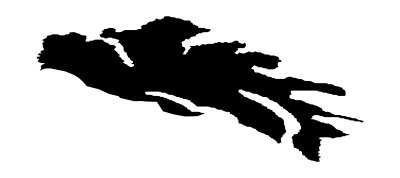

```mathematica
Polygon[Reverse/@Take[gdata2[[1,1,1]],{1,-1,2}]]//Graphics
```

```mathematica
Graphics[gdata2[[1]]]
```

-Graphics-